```mathematica
img=Import["C:\\Users\\ray81\\Desktop\\Computer Graphics\\Doge.jpeg"];
imgc=ImageForwardTransformation[img,Through[{Re,Im}[(#[[1]]+I #[[2]])^3]]&,Background->1,DataRange->{{-1,1},{-1,1}},PlotRange->{{-2,2},{-2,2}}]
ParametricPlot[{Re[(x+I y)^3],Im[(x+I y)^3]},{x,-1,1},{y,-1,1},PlotStyle->FaceForm[None],Prolog->{Texture[imgc],Polygon[Scaled/@{{0,0},{1,0},{1,1},{0,1}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]}]
```

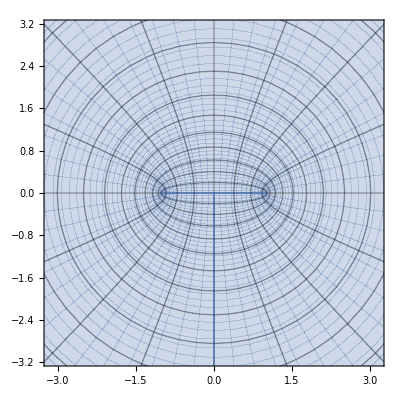

```mathematica
ParametricPlot[{Sin[x]Cosh[y],Cos[x]Sinh[y]},{x,-Pi,Pi},{y,0,Pi},PlotRange->{{-Pi,Pi},{-Pi,Pi}},Mesh->15]
```

```mathematica
img=Import["C:\\Users\\ray81\\Desktop\\Computer Graphics\\Doge.jpeg"];
img2=Colorize[img,ColorFunction->"Rainbow"]
imgc=ImageForwardTransformation[img2,Through[{Re,Im}[((#[[1]]+I #[[2]])-2)/(1-2*(#[[1]]+I #[[2]]))]]&,Background->1,DataRange->{{-1,1},{0,3}},PlotRange->{{-1.8,0.4},{-1.22,0.21}}]
ParametricPlot[{Re[(x+I y-2)/(1-2*(x+ I y))],Im[(x+I y-2)/(1-2*(x+ I y))]},{x,-1,1},{y,0,3},PlotStyle->FaceForm[None],Prolog->{Texture[imgc],Polygon[Scaled/@{{0,0},{1,0},{1,1},{0,1}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]}]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
img=ExampleData[{"TestImage","Mandrill"}];
imgc=ImageForwardTransformation[img,Through[{Re,Im}[(#[[1]]+I #[[2]])^3]]&,Background->1,DataRange->{{-1,1},{-1,1}},PlotRange->{{-2,2},{-2,2}}];
```

```mathematica
ParametricPlot[{Re[(x+I y)^3],Im[(x+I y)^3]},{x,-1,1},{y,-1,1},ColorFunction-> "DarkRainbow",PlotStyle->FaceForm[None],Prolog->{Texture[imgc],Polygon[Scaled/@{{0,0},{1,0},{1,1},{0,1}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]}]
```

```mathematica
img=Import["C:\\Users\\ray81\\Desktop\\Computer Graphics\\Doge.jpeg"];
img2=Colorize[img,ColorFunction->"Rainbow"]
imgc=ImageForwardTransformation[img2,Through[{Re,Im}[I*(1-(#[[1]]+I #[[2]]))/(1+(#[[1]]+I #[[2]]))]]&,Background->1,DataRange->{{-1,1},{-1,1}},PlotRange->{{-2,2},{-2,2}}]
```

-Graphics-

-Graphics-

```mathematica
img=Import["C:\\Users\\ray81\\Desktop\\Computer Graphics\\DogeCircle.png"];
img2=Colorize[img,ColorFunction->"Rainbow"]
imgc=ImageForwardTransformation[img2,Through[{Re,Im}[Log[#[[1]]+I #[[2]]]]]&,Background->1,DataRange->{{-3,3},{-3,3}},PlotRange->{{0,Log[3]},{-3,3}}]
```

-Graphics-

-Graphics-

```mathematica
ParametricPlot[{Sin[x]Cosh[y],Cos[x]Sinh[y]},{x,-Pi,Pi},{y,0,Pi},PlotRange->{{-Pi,Pi},{-Pi,Pi}},Mesh->15]
```

```mathematica
img2=Import["C:\\Users\\ray81\\Desktop\\Computer Graphics\\3d-Earth-Globe.png"]
imgc=ImageForwardTransformation[img2,Through[{Re,Im}[Log[#[[1]]+I #[[2]]]]]&,Background->1,DataRange->{{-3,3},{-3,3}},PlotRange->{{-Log[5],Log[5]},{-3.14,3.14}}]
```

-Graphics-

-Graphics-

```mathematica
k
```

```mathematica
ParametricPlot[{Sin[x]Cosh[y],Cos[x]Sinh[y]},{x,-Pi,Pi},{y,0,Pi},PlotRange->{{-Pi,Pi},{-Pi,Pi}},Mesh->15]
```

-Graphics-

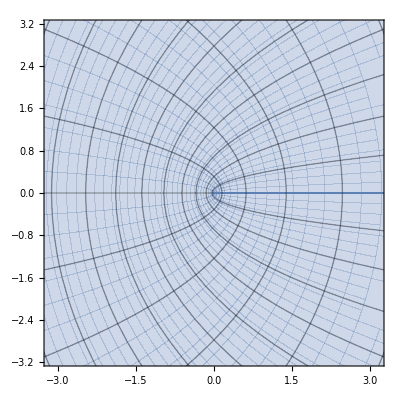

```mathematica
ParametricPlot[{x^2-y^2,2*x*y},{x,-Pi,Pi},{y,0,Pi},PlotRange->{{-Pi,Pi},{-Pi,Pi}},Mesh->15]
```

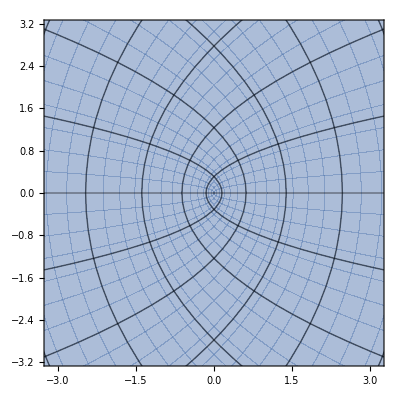

```mathematica
ParametricPlot[{x^2-y^2,2*x*y},{x,-Pi,Pi},{y,-Pi,Pi},PlotRange->{{-Pi,Pi},{-Pi,Pi}},Mesh->15]
```

```mathematica
ParametricPlot[{Exp[x]Cos[y],Exp[x]Sin[y]},{x,-Pi,Pi},{y,-Pi,Pi},PlotRange->{{-Pi,Pi},{-Pi,Pi}},Mesh->15]
```

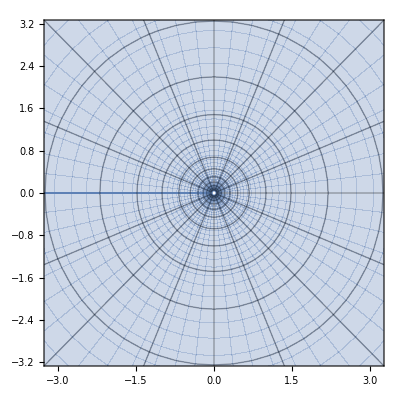
```mathematica
-Graphics-
ParametricPlot[{Exp[x]Cos[y],Exp[x]Sin[y]},{x,-Pi,Pi},{y,-Pi,Pi},PlotRange->{{-Pi,Pi},{-Pi,Pi}},Mesh->15]
```

```mathematica
Re[ComplexExpand[χ/(1+I ω τ)]]
```

Im[(τ χ ω)/(1+τ^2 ω^2)]+Re[χ/(1+τ^2 ω^2)]

```mathematica
Re[ComplexExpand[a+b I]]
```

-Im[b]+Re[a]

```mathematica
Re[ComplexExpand[3+2 I]]
```

3

```mathematica
Re[ComplexExpand[a+b I]]
```

-Im[b]+Re[a]

```mathematica
Re[ComplexExpand[1/2*(x+I y+1/(x+I y))]]
```

-Im[y/2-y/(2 (x^2+y^2))]+Re[x/2+x/(2 (x^2+y^2))]

```mathematica
Im[ComplexExpand[1/2*(x+I y+1/(x+I y))]]
```

Im[x/2+x/(2 (x^2+y^2))]+Re[y/2-y/(2 (x^2+y^2))]

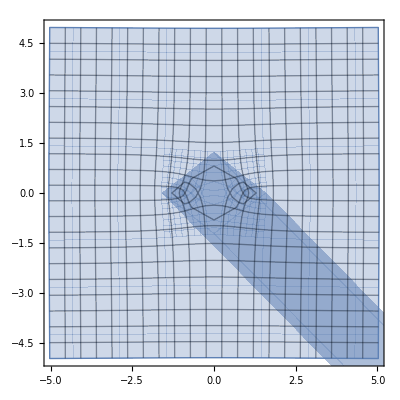

```mathematica
ParametricPlot[{x/2+x/(2 (x^2+y^2)),y/2-y/(2 (x^2+y^2))},{x,-10,10},{y,-10,10},PlotRange->{{-5,5},{-5,5}},Mesh->20]
```

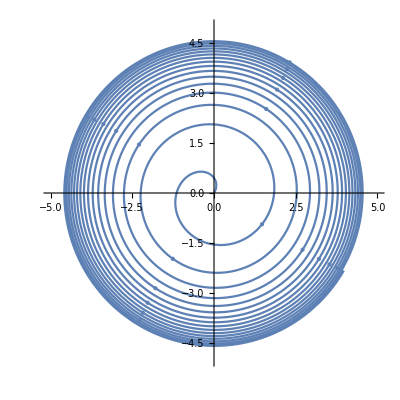

```mathematica
PolarPlot[Log[r],{r ,1,100},PlotRange->{{-5,5},{-5,5}},Mesh->20]
```

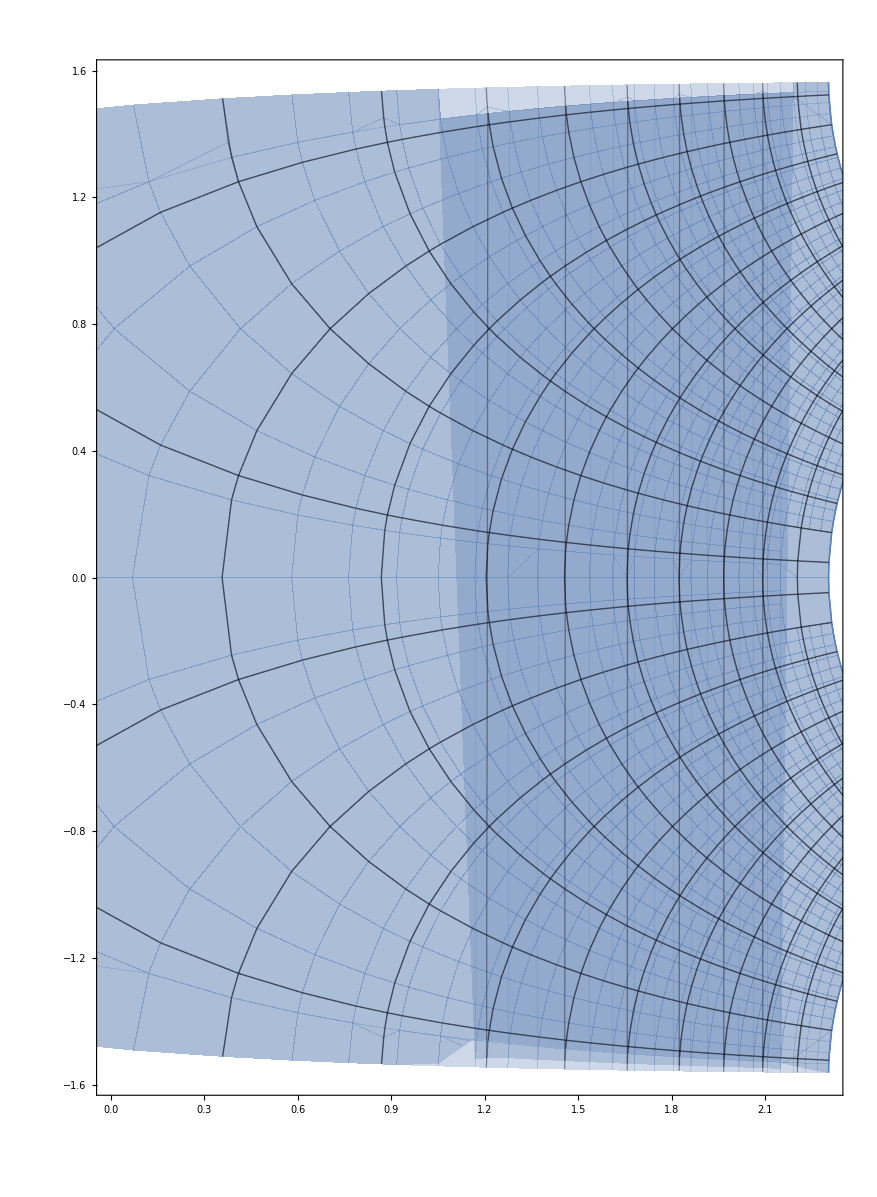

```mathematica
ParametricPlot[{Log[(x^2+y^2)^(1/2)],ArcTan[y/x]},{x,-10,10},{y,-10,10},PlotRange->{{0,Log[10]},{-Pi/2,Pi/2}},Mesh->20]
```